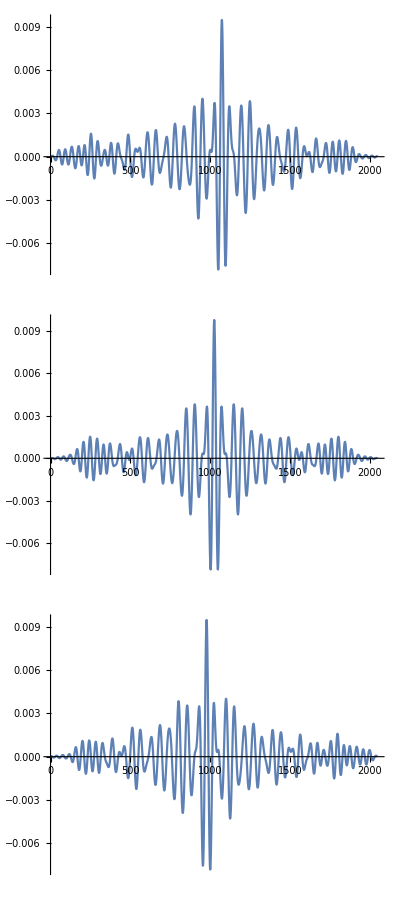

{{0.00947166,{-50}},{0.00978027,{-2}},{0.00947166,{46}}}

48.

```mathematica
data=Import["/tmp/xcorr_test.tsv"]//Transpose;
lengthFT=2048;
nSamples=Dimensions[data][[2]];
nChannels=Dimensions[data][[1]];

Table[
ListLinePlot[data[[i,nSamples-lengthFT;;]],PlotRange->All],
{i,nChannels}]//TableForm

Table[{Max[data[[i,nSamples-lengthFT;;]]],lengthFT/2-Ordering[data[[i,nSamples-lengthFT;;Length[data[[i]]]]],-1]},{i,nChannels}]
3.43/343. 4800
```